# 私の血糖値の推移

### 経緯

1月末に、かかりつけ医にて重度の糖尿病症状が確認され直ちに入院となった。
状態は重度の糖尿病性ケトアシドーシス（極度の脱水、栄養失調、ケトーシス、高血糖）。昏睡していてもおかしくない状態だったらしい。
2週間の入院。治療は脱水状態の離脱からはじめられ、数日後より栄養状態の回復治療、ついで糖尿病治療を行なった。同時に合併症検査が行われた。
結果的に合併症はなし、退院後はインスリンによる治療と定期的な通院検査を行うものとなった。

退院後の治療は食前のインスリン投与、1日1回の高濃度インスリン投与、カロリーコントロール、血糖コントロール、を行う。

血糖は血糖測定器があり随時測定可能。食事前に血糖測定を行なっている。

本日は血糖値の測定についてと血糖値の推移について報告する。
- 周期性の確認
- ローパスによる血糖値の長期変動

### 血糖値の測定

```mathematica
jpg="/Users/kouamano/Profile/IMG_0085.jpg"
```

/Users/kouamano/Profile/IMG_0085.jpg

下の写真が血糖値の測定器（左が測定器とチップ、右が穿刺具と穿刺針）。

血糖値の測定は、まず穿刺具にて指先に穿刺し、血液を測定器のチップに塗布する。数秒で結果が出る。

測定器には過去数十件の値と測定時間が記録されており、NFCによりスマホに転送可能。転送されたスマホ側でエクセルデータを作成しさらにメール転送が可能。

```mathematica
Import[jpg]
```

-Graphics-

### Data

スマホから転送されてきたデータのファイル。

```mathematica
dir="/Users/kouamano/Profile/"
```

/Users/kouamano/Profile/

```mathematica
xlsfile="02_15_2022-05_15_2022.xls"
```

02_15_2022-05_15_2022.xls

### Import

ファイルから値を読み取る。

```mathematica
importData=Import[dir<>xlsfile];
```

```mathematica
selectedData[1]=Transpose[Transpose[Drop[importData[[1]],1]][[{1,3}]]];
```

```mathematica
ts=TimeSeries[selectedData[1]]
```

TimeSeries[…]

単純なプロット。

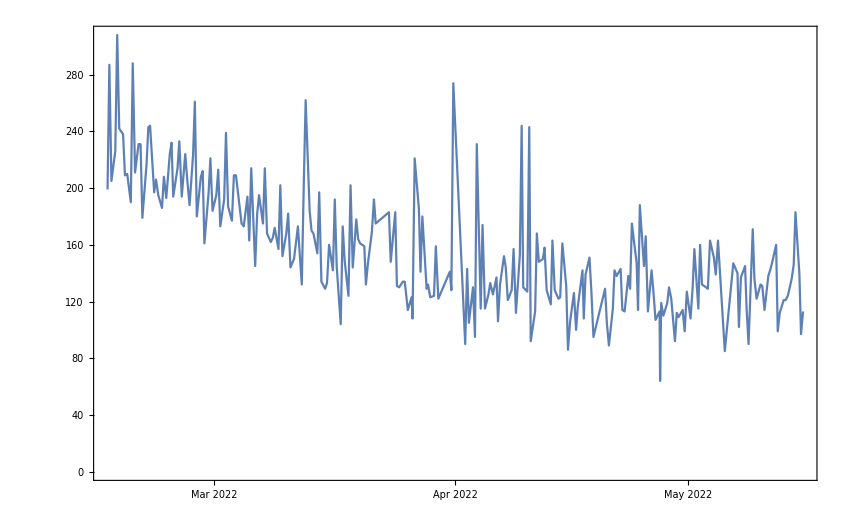

```mathematica
dlp=DateListPlot[ts]
```

### Interpolation

測定間隔がまばらなので間の値も推測できるよう補間関数を作成。

```mathematica
nts=Normal[ts];
```

```mathematica
nPts=Length[nts]
```

253

```mathematica
startDate=nts[[1,1]]
```

Tue 15 Feb 2022 06:18:00GMT+9

```mathematica
startTime=AbsoluteTime[nts[[1,1]]]
```

3853894680

```mathematica
endDate=nts[[-1,1]]
```

Sun 15 May 2022 17:59:00GMT+9

```mathematica
endTime=AbsoluteTime[nts[[-1,1]]]
```

3861626340

```mathematica
period=(endTime-startTime)/nPts//N
```

30559.9

```mathematica
endDate-startDate
```

89.4868 days

```mathematica
nPts/(endDate-startDate)
```

2.82723 per day

```mathematica
ifn=Interpolation[ts]
```

InterpolatingFunction[…]

### Fourier

period 1

実際の測定回数から平均の測定間隔を算出し用いる。うまくいっているか確認。おおむね良いだろうと判断。

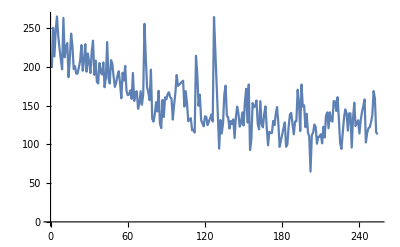
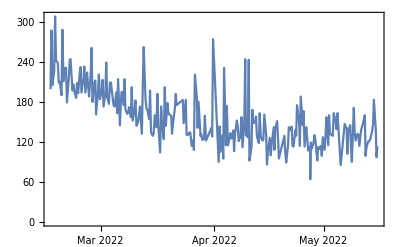
Interporation | -Graphics-
Original | -Graphics-

```mathematica
Grid[{{"Interporation",ListLinePlot[Table[ifn[t],{t,startTime,endTime,period}]]},{"Original",dlp}}]
```

等間隔データに対してフーリエを適応する。低周波側に大きなピークが見られる。このような場合、強い周期性がないことを示唆している。

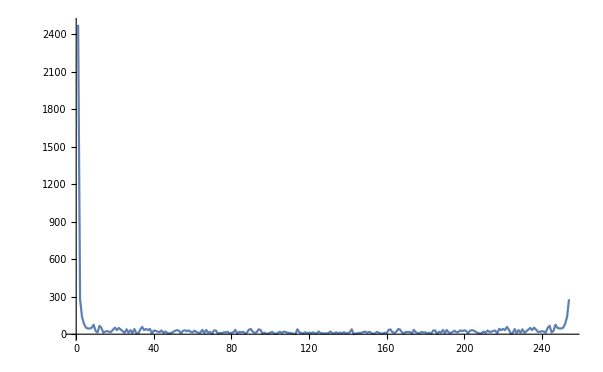

```mathematica
ListLinePlot[(fou=Fourier[Table[ifn[t],{t,startTime,endTime,period}]])//Abs,PlotRange->Full]
```

低周波側を除き、ある程度の強度がある周波数を確認する。20回弱、80回後の部分にピークが見られる。

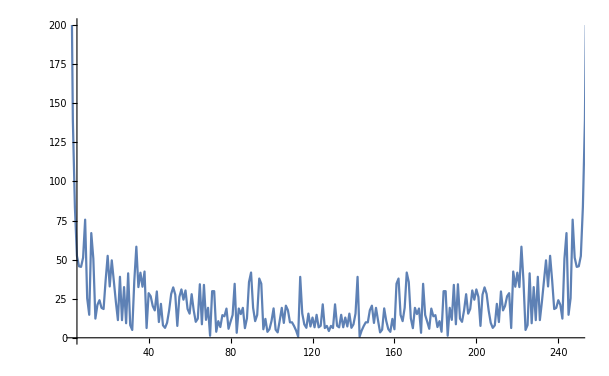

```mathematica
ListLinePlot[Fourier[Table[ifn[t],{t,startTime,endTime,period}]]//Abs,PlotRange->{{5,nPts-5},{0,200}}]
```

```mathematica
af=Abs[Fourier[Table[ifn[t],{t,startTime,endTime,period}]]];
```

```mathematica
max=Max[af[[5;;nPts-5]]]
```

75.5509

```mathematica
Position[af,max]
```

{{9},{247}}

8回の繰り返し、11日の周期。

```mathematica
(endTime-startTime)/60/60/24/(9-1)//N
```

11.1859

もう一つ、30~40回前後の部分にピークが見られる。

```mathematica
TakeLargest[af[[5;;nPts-5]],9]
```

{75.5509,75.5509,66.9704,66.9704,58.2689,58.2689,52.431,52.431,52.2838}

```mathematica
max2=TakeLargest[af[[5;;nPts-5]],3][[-1]]
```

66.9704

```mathematica
Position[af,max2]
```

{{12}}

11回の繰り返し、8.9日周期。

```mathematica
(endTime-startTime)/60/60/24/(11-1)//N
```

8.94868

period 2

1日4回の測定データを擬似的に作成。（おおよそ6、12、18時に測定しているので、24時の測定値を仮想的に作る）

```mathematica
period2=(endTime-startTime)/(endDate-startDate)[[1]]/4 (*1日4回*)
```

21600.

```mathematica
nPts2=Ceiling[(endTime-startTime)/period2]
```

358

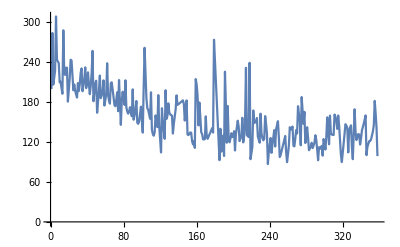
Interpolation | -Graphics-
Original | -Graphics-

```mathematica
Grid[{{"Interpolation",ListLinePlot[Table[ifn[t],{t,startTime,endTime,period2}]]},{"Original",dlp}}]
```

あまり変わらない。20回前後の周波数の方が強くなった。

```mathematica
fou2=Fourier[Table[ifn[t],{t,startTime,endTime,period2}]];
```

```mathematica
largest2=TakeLargest[Abs[fou2[[5;;(nPts2-5)]]],10]
```

{92.4709,92.4709,72.3749,72.3749,70.7049,70.7049,68.9435,66.3431,66.3431,62.5661}

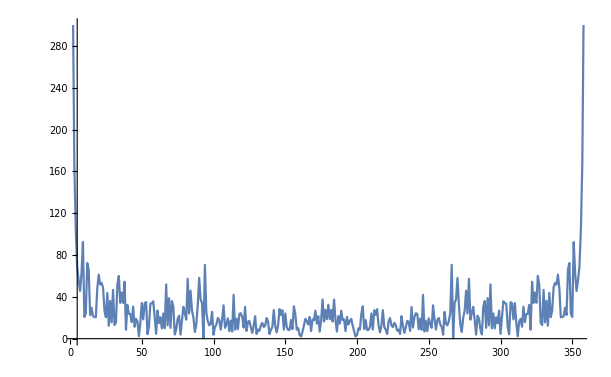

```mathematica
ListLinePlot[Fourier[Table[ifn[t],{t,startTime,endTime,period2}]]//Abs,PlotRange->{{5,nPts2-5},{0,300}}]
```

```mathematica
Peak2[1]=largest2[[1]]
```

92.4709

```mathematica
Position[Abs[fou2],Peak2[1]]
```

{{9}}

### ローパス

period 1

まず、逆フーリエで再現できるか確認。

```mathematica
Grid[{{"InverseFourier",ListLinePlot[InverseFourier[fou],PlotRange->Full]},{"Original",dlp}}]
```

InverseFourier | -Graphics-
Original | -Graphics-

少しづつ、ローパスをかけていく。

```mathematica
fouLen=Length[fou]
```

254

```mathematica
np=150
```

150

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(flt["total"]=Flatten[{flt[1],flt[2]}])//Length
```

254

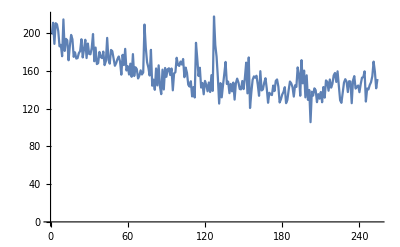

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
np=100
```

100

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(flt["total"]=Flatten[{flt[1],flt[2]}])//Length
```

254

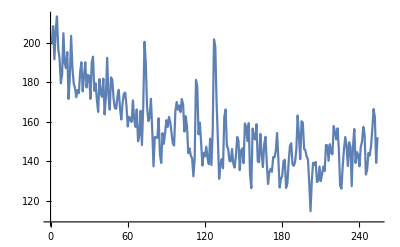

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
np=50
```

50

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
fullLen=((flt["total"]=Flatten[{flt[1],flt[2]}])//Length)
```

254

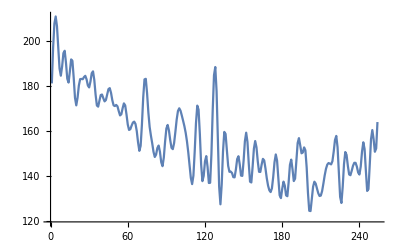

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
np=20
```

20

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(flt["total"]=Flatten[{flt[1],flt[2]}])//Length
```

254

18回の繰り返しと右肩下がりの傾向が見える。

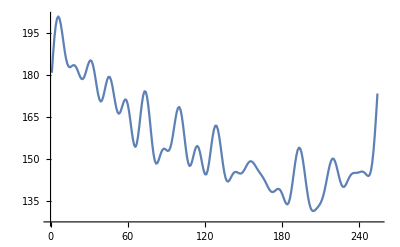

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
InverseFourier[fou*flt["total"]]//Length
```

254

### EQ

補間データに対してエコライザーを通す。

period 1

7帯域とする。

```mathematica
fullLen
```

254

```mathematica
step2=(7-1)/fullLen//N
```

0.023622

フィルターのポイント数を合わせる。

```mathematica
Table[1,{t,1,7-step2,step2}]//Length
```

254

フィルターの確認

```mathematica
Manipulate[ListPlot[Table[Interpolation[{x1,x2,x3,x4,x5,x6,x7}][t],{t,1,7-step2,step2}]],{x1,0,1},{x2,0,1},{x3,0,1},{x4,0,1},{x5,0,1},{x6,0,1},{x7,0,1}]
```

フィルターの適応

```mathematica
Manipulate[ListLinePlot[Abs[InverseFourier[fou*Table[Interpolation[{x1,x2,x3,x4,x5,x6,x7}][t],{t,1,7-step2,step2}]]]],{x1,0,1},{x2,0,1},{x3,0,1},{x4,0,1},{x5,0,1},{x6,0,1},{x7,0,1}]
```

フィルターと波形を同時表示。

```mathematica
Manipulate[{ListPlot[Table[Interpolation[{x1,x2,x3,x4,x5,x6,x7}][t],{t,1,7-step2,step2}]],ListLinePlot[Abs[InverseFourier[fou*Table[Interpolation[{x1,x2,x3,x4,x5,x6,x7}][t],{t,1,7-step2,step2}]]]]},{x1,0,1},{x2,0,1},{x3,0,1},{x4,0,1},{x5,0,1},{x6,0,1},{x7,0,1}]
```